# Projekt za Računalniška orodja v matematiki

23.3.2021

## Podatki, ki jih bomo uporabili

```mathematica
drzave=EntityList["Country"];
```

Povprečne mesečne, sezonske in pa letne temperature. (To bom dopolnil še kasneje.)

Uvozil bom podatke iz excela, ki povedo kolikšna je letna anomalija na svetovnem merilu glede na povprečje 20. stoletja, pridobljeni so pa na:

```mathematica
Hyperlink["https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021"]
```

https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021

```mathematica
podatkiIzExcela = Import["C:\\Users\\ALEN\\Desktop\\FMF\\ROM\\Projekt_ROM_github\\data.csv", "Dataset"];
```

```mathematica
podatkiOSloveniji = Import["C:\\Users\\ALEN\\Desktop\\FMF\\ROM\\Projekt_ROM_github\\povprečne_letne_temperature_slovenije.csv","Dataset"];
```

```mathematica
podatkiIzExcelaVTabeli = podatkiIzExcela[[6;;All ]] //TableForm;
```

```mathematica
podatkiOSlovenijiVTabeli = podatkiOSloveniji[[4;;All ]] //TableForm;
```

## Globalno

```mathematica
seznamAnomalijTemperatur=Table[podatkiIzExcelaVTabeli[[1]][[i]][[2]],{i,1,Length[podatkiIzExcelaVTabeli[[1]]]}];
```

Prikaz anomalij globalne temperature od leta 1880 do leta 2020.

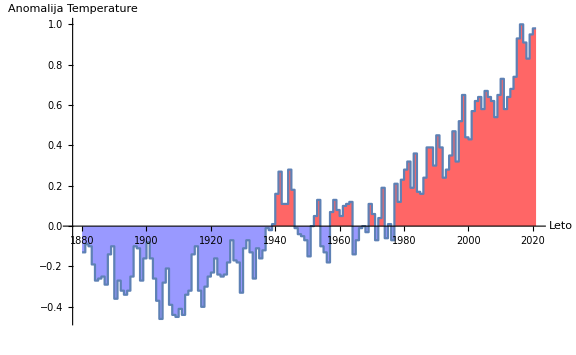

```mathematica
ListStepPlot[{seznamAnomalijTemperatur},DataRange->{1880, 2020},ImageSize->Large,AxesLabel->{"Leto","Anomalija Temperature"},Filling->Axis,FillingStyle->{Opacity[0.4,Blue], Opacity[0.6,Red]}]
```

## Slovenija

Poglejmo letne povprečne temperature za Slovenijo med leti 2001 in 2014.

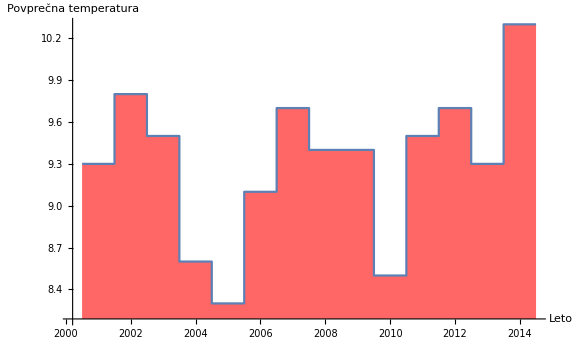

```mathematica
seznamPovprecnihTemperatur = Table[podatkiOSlovenijiVTabeli[[1]][[i]][[3]],{i,1,Length[podatkiOSlovenijiVTabeli[[1]]]}];
ListStepPlot[seznamPovprecnihTemperatur,Center,DataRange->{2001,2014},ImageSize->Large,AxesLabel->{"Leto","Povprečna temperatura"},Filling->Axis,FillingStyle->Opacity[0.6,Red]]
```